# Problem 1: question 2.4. for uphill and downhill motions. Problem 2: Reproducing Fig. 2.7 for the cases (a) no wind (b) headwind (c) tailwind. (d) comparing output to NDSolve Problem 3: question 2.7. (a) using the isothermal model to reproduce Fig. 2.5. (b) using the adiabatic model to compare with the isothermal model. (c) Taking θ = π/4 to study the temperature effect on the kinematics for T = 250, 275, 300 and 325 K. NB: I Compare using NDSolve whenever applicable.

## Problem 1

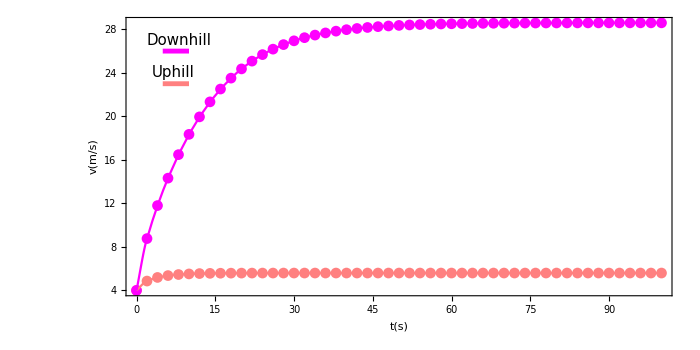

```mathematica
ClearAll["Global`*"]

(* Initializations *) 
 color = {Pink,Magenta};(*since we have 2 curves I'll pick 2 different colors*)
m=70; c=0.5;v0=4; dt=2;a=0.33 ;p=400;ρ=1.22 ;(*air density at sea level*)
 grad=0.1 (*steepness*); ϕ=ArcTan[0.1]; grav={-9.81,9.81} ; lgrav=Length[grav];(*for up and downhill +/- *);tStart=0;tEnd=100; 

(*all values taken from the example in the book *)
(*form of the v was derived by solving for forces down or up the hill and considering both drag, gravity and cyclist's force*)
(*ⅆv/ⅆt==(P/(m v(t))-(A c ρ v^2)/(2 m))±g sin(θ)->v(Δt+t)==(((Δt P)/(m v(t))-(A c Δt ρ v^2)/(2 m))±Δt g sin(θ))+v(t)*)

p7= Table[0,{i,lgrav }];
p7a= Table[0,{i,lgrav }];

Do[

(*setting initial conditions*)
tList = Range[tStart,tEnd,dt]; lt = Length[tList];
vList = Table[0,{i,lt}];
p5b=  Table[0,{i,lgrav }]; (* Trajectory plots for diff wind situations *)
vList[[1]] = v0;
Do[vList[[nt]]   =vList[[nt-1]]+ (p dt)/(m *vList[[nt-1]])- (a c ρ (vList[[nt-1]])^2 dt)/(2 *m) + grav[[ngrav]] Sin[ϕ] dt ,{nt,2,lt}];
vtList =Table[{tList[[j]],vList[[j]]},{j,lt}]; (* CAREEE the x axis is the first entry in the brackets *)
p5 =ListPlot[vtList,PlotStyle->color[[ngrav]]];
p7[[ngrav]] =p5;

(*now to do the same using the built in ND solve finction*)
solProj = NDSolve[{v'[t]==((p/(m v[t])-(a c ρ v[t]^2)/(2 m))+grav[[ngrav]] Sin[ϕ]),v[0]==4},v,{t,tStart,tEnd},StartingStepSize->dt,Method->{"FixedStep",Method->"ExplicitEuler"}];
(*The plotting step using the normal plot function instead and extracting values from the function we got out of NDSolve v[t] as opposed to using tables and list plot where our results are distinct points in a table, so here we specify a starting poit for the independent variable and an ending point*)
p5a=Plot[v[t]/.solProj,{t,tStart,tEnd},PlotRange->All,PlotStyle->color[[ngrav]]];
p7a[[ngrav]]=p5a,


{ngrav,1,lgrav}];



(*code for the legend, a red and pink line at positions given by 2 coordinates for the start and end of the line*)
g2=Graphics[{Magenta,Thickness[0.005],Line[{{5,26},{10,26}}]}];
g3=Graphics[{Pink,Thickness[0.005],Line[{{5,23},{10,23}}]}];
(*the directive function allows me to adjust more than one option for the labelstyle*)
Show[g2,g3,p7,p7a, PlotRange->All,Frame -> True,FrameLabel->{Style["t(s)",Large],Style["v(m/s)",Large]},LabelStyle->Directive[20,Black],ImageSize->700 ,AspectRatio->0.5,
Epilog->{Inset[Style["Downhill",15] ,{8,27}],Inset[Style["Uphill",15],{7,24}]}]
```

We can clearly see the solid line (NDSolve solution) and our coded Euler solution (dots)

## Problem 2a, b and c

before we start we need to calculate the F drag terms for both x and y and get a modified expression for (dv_(x,y))/dt that is considerate of both drag and wind speeds, the new expression will in turn be used to solve for velocity terms in our 4 ODEs we get from reducing the projectile equations of motion. NB: The general form of the do loops was extracted from the Dr’s lecture which you’d sent us, and I will in turn modify and build on it. v_wind in the question was given to be only along x, so it will be included only in v_x calculations and it has a norm of v_wind as well so no square-rooting, it will be directly deducted or added to v_norm.

```mathematica
ClearAll["Global`*"]

(* Initializations *) 
 color = {Pink,Magenta,Red};(*since we have 3 curves I'll pick 3 different colors*)

 grav = 9.8; tmax = 100; v0 = 49 ;
(*49 meters per second which is equivalent to 110 mph as stated in the question since im using SI units*)

vWind={0,4.471,-4.471} ;lvWind=Length[vWind];

(*since the drage here is not constant, we will have to use the analytical approximation for the ball mentioned in the text, which is a function of velocity.*)

x0 = 0.0; y0 =0.0; 
θ=35*(π/180.0); (*angle in radians, we chooose an angle of 35 as stated in the example*)
dt = 0.2;
p7 = Table[0,{i,lvWind }];

Do[  (* Trajectory plots for diff wind situations *)
vx0 = v0 Cos[θ]; vy0 = v0 Sin[θ];

tList = Range[0,100,dt]; lt = Length[tList];
vxList = Table[0,{i,lt}]; vyList = vxList; xList =vxList;yList = vxList;b2mList=vxList;(*setting all tables to zero with the same size as the time list*)
(*setting initial conditions*)
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 
b2mList[[1]]=0.0039+0.0058/(1+Exp[((v0-vWind[[ndWind]]-35)/5)]);
Do[
xList[[nt]]   = xList[[nt-1]] + vxList[[nt-1]] dt; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt-1]] dt;
vNorm :=  Sqrt[vxList[[nt-1]]^2+vyList[[nt-1]]^2];(* these are the same as for no wind cases we covered in lecture, since x and y position is not an explicit function of drag and wind effect, they act through velocity and wil be seen in the following few equations for Subscript[v, y] and Subscript[v, x], Expressions for Subscript[v, x] and Subscript[v, y] were obtained by solving newton's secod law
whilst considering Forces from drag, in both x and y, gravity in y, and wind speed which adds or subtracts from the speed of the ball in given in x only*)
vxList[[nt]] =vxList[[nt-1]] - (b2mList[[nt-1]]*Abs[vNorm-vWind[[ndWind]]]*(vxList[[nt-1]]-vWind[[ndWind]])* dt );
vyList[[nt]] =vyList[[nt-1]] - ((grav+(b2mList[[nt-1]]*Abs[vNorm-vWind[[ndWind]]]*(vyList[[nt-1]])))* dt );
b2mList[[nt]]=0.0039+0.0058/(1+Exp[((Sqrt[vxList[[nt]]^2+vyList[[nt]]^2]-vWind[[ndWind]]-35)/5)]); (*with every iteration of nt we update b2m since it is a function of vNorm *)
If[yList[[nt]]>0,nRange = nt] (* time when x = Range, y = 0 *)
,{nt,2,lt}];
xylist =Table[{xList[[j]],yList[[j]]},{j,nRange}];
p5 =ListPlot[xylist,PlotStyle->color[[ndWind]]];
 p7[[ndWind]] =p5,{ndWind,lvWind}](*every iteration adds the resultant p5 for a certain ndWind value to a list of list plots to combine them all in one plot*)
```

The graphics in the mauve cells are coded such that we get 3 lines, one for each wind condition, and a legend. The graphics command was used and within first the color was specified, the thickness, then the graphic, I wanted lines for the legend, so I used Line function which in turn took arguments for each point which will be connecting specified line segments.

```mathematica
g2=Graphics[{Red,Thickness[0.005],Line[{{6,29},{21,29}}]}];
g3=Graphics[{Pink,Thickness[0.005],Line[{{6,27},{21,27}}]}];
g4=Graphics[{Magenta,Thickness[0.005],Line[{{6,25},{21,25}}]}];
```

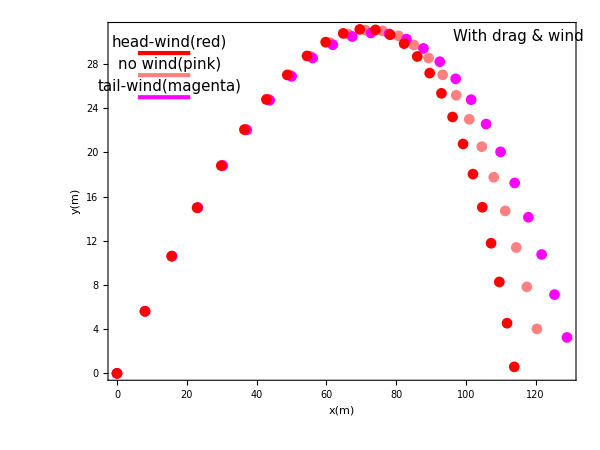

```mathematica
Show[g2,g3,g4,p7, PlotRange->All,Frame -> True,FrameLabel->{Style["x(m)",Large],Style["y(m)",Large]},LabelStyle->Directive[20,Black],ImageSize->600 ,AspectRatio->0.75,
Epilog->{Inset[Style["With drag & wind",15] ,{115,30.5}],Inset[Style["head-wind(red)",15],{15,30}], Inset[Style["no wind(pink)",15] ,{15,28}],Inset[Style["tail-wind(magenta)",15] ,{15,26}]}]
```

## Problem 2d

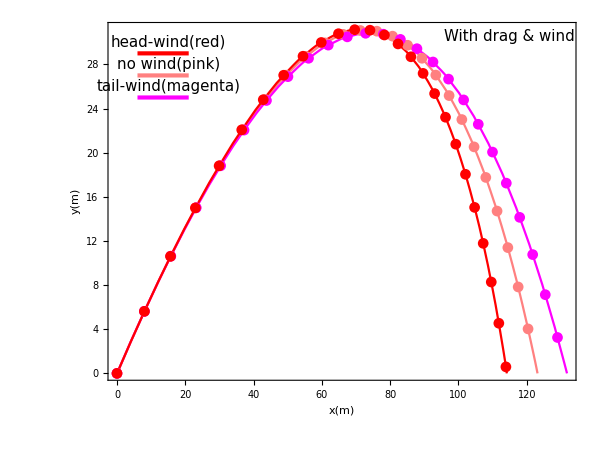

```mathematica
(* Initializations *) 
 color = {Pink,Magenta,Red};(*since we have 3 curves I'll pick 3 different colors*)

 grav = 9.8; tmax = 100; v0 = 49 ;
vWind={0,4.471,-4.471} ;lvWind=Length[vWind];

x0 = 0.0; y0 =0.0; 
θ=35*(π/180.0); (*angle in radians, we chooose an angle of 35 as stated in the example*)
dt = 0.2;

p5b=  Table[0,{i,lvWind }]; (* Trajectory plots for diff wind situations *)
Do[ 
vx0 = v0 Cos[θ]; vy0 = v0 Sin[θ];
b2m[t_]:=0.0039+0.0058/(1+Exp[((√((Subscript[v, x][t])^2+(Subscript[v, y][t])^2)-vWind[[ndWind]]-35)/5)]); (*to use NDsolve her we must specify b2m as an explicit function of t*)
solProj = NDSolve[{x'[t]==Subscript[v, x][t],Subscript[v, x]'[t]==-b2m [t]*(Subscript[v, x][t]-vWind[[ndWind]])*( Abs[ √((Subscript[v, x][t])^2+(Subscript[v, y][t])^2)-vWind[[ndWind]]]),y'[t]==Subscript[v, y][t],Subscript[v, y]'[t]==-grav-(b2m[t]* Subscript[v, y][t] *( Abs[ √((Subscript[v, x][t])^2+(Subscript[v, y][t])^2)-vWind[[ndWind]]])),x[0]==0.,y[0]==0.,Subscript[v, x][0]==vx0, Subscript[v, y][0]==vy0,WhenEvent[y[t]== 0.0,end = t]},{x,y},{t,tmax},StartingStepSize->dt,Method->{"FixedStep",Method->"ExplicitEuler"}];
p5b[[ndWind]] =ParametricPlot[Evaluate[{x[t],y[t]}/.solProj],{t,0,end},PlotStyle->color[[ndWind]]],{ndWind,lvWind }]

(*I will include here the graphics I'd set up previously and the solution p7 with the 3 plots from part a b and c*)

pWDall =Show[g2,g3,g4,p5b,p7, PlotRange->All,Frame -> True,FrameLabel->{Style["x(m)",Large],Style["y(m)",Large]},LabelStyle->Directive[20,Black],ImageSize->600 ,AspectRatio->0.75,
Epilog->{Inset[Style["With drag & wind",15] ,{115,30.5}],Inset[Style["head-wind(red)",15],{15,30}], Inset[Style["no wind(pink)",15] ,{15,28}],Inset[Style["tail-wind(magenta)",15] ,{15,26}]}]
```

The figure below clearly shows the match between the ND solve solution (solid lines) and the coded Euler solution in part a b and c.

## Problem 3a

```mathematica
ClearAll["Global`*"]

(* Initializations *) 
 color = {Red,Magenta,Orange,Yellow};(*since we have 3 curves I'll pick 3 different colors*)

 grav = 9.8; tmax = 100; v0 = 700 ;
(*49 meters per second which is equivalent to 110 mph as stated in the question since im using SI units*)

θ={35,45}*(π/180.0) ;lθ=Length[θ];
b2m=4*10^-5;
yy=1*10^4;
x0 = 0.0; y0 =0.0; 
 (*angle in radians, we chooose an angle of 35 as stated in the example*)
dt = 1;
p7 = Table[0,{i,lθ }];
p7a = Table[0,{i,lθ }];
p72= Table[0,{i,lθ }];
p7a2 = Table[0,{i,lθ }];


Do[ 
vx0 = v0 Cos[θ[[nθ]]]; vy0 = v0 Sin[θ[[nθ]]];
tList = Range[0,100,dt]; lt = Length[tList];
(*-----------------------------------The isothermal part loop with a unique b2m-----------------------------------------------------------------------*)
vxList = Table[0,{i,lt}]; vyList = vxList; xList =vxList;yList = vxList;b2mList=vxList;(*setting all tables to zero with the same size as the time list*)
(*setting initial conditions*)
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 
b2mList[[1]]=b2m;

Do[
xList[[nt]]   = xList[[nt-1]] + vxList[[nt-1]] dt; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt-1]] dt;
vNorm =  Sqrt[vxList[[nt-1]]^2+vyList[[nt-1]]^2];(* these ......................................................................x only*)
vxList[[nt]] =vxList[[nt-1]] - (b2mList[[nt-1]]* vNorm*(vxList[[nt-1]])* dt );
vyList[[nt]] =vyList[[nt-1]] - ((grav+(b2mList[[nt-1]]*vNorm*(vyList[[nt-1]])))* dt );
b2mList[[nt]]=b2m*Exp[(-yList[[nt]])/yy]; (*with every iteration of nt we update b2m since it is a function of vNorm *)
If[yList[[nt]]>0,nRange = nt],{nt,2,lt}];
xylist =Table[{xList[[j]],yList[[j]]},{j,nRange}];
p5 =ListPlot[xylist/1000.0,PlotStyle->color[[nθ]]];
solProj = NDSolve[{x'[t]== vx[t],y'[t]==vy[t], vx'[t]==-b2m* Exp[(-y[t])/yy] *√((vx[t])^2+(vy[t])^2)*(vx[t]),vy'[t]== -b2m* Exp[(-y[t])/yy] *√((vx[t])^2+(vy[t])^2)*vy[t]-grav, x[0]==x0, y[0]==x0, vx[0]== vx0, vy[0]==vy0,WhenEvent[y[t]== 0,end = t]},{x,y},{t,tmax},StartingStepSize->dt,Method->{"FixedStep",Method->"ExplicitEuler"}];

(*-----------------------------------------The no correction part loop-----------------------------------------------------------------*)

vx2List = Table[0,{i,lt}]; vy2List = vx2List; x2List =vx2List;y2List = vx2List;
vx2List[[1]] = vx0; vy2List[[1]] = vy0; 
x2List[[1]]   = x0;   y2List[[1]]    = y0; 
Do[
x2List[[nt]]   = x2List[[nt-1]] + vx2List[[nt-1]] dt; 
y2List[[nt]]   = y2List[[nt-1]] + vy2List[[nt-1]] dt;
v2Norm =  Sqrt[vx2List[[nt-1]]^2+vy2List[[nt-1]]^2];
vx2List[[nt]] =vx2List[[nt-1]] - (b2m* v2Norm*(vx2List[[nt-1]])* dt );
vy2List[[nt]] =vy2List[[nt-1]] - ((grav+(b2m*v2Norm*(vy2List[[nt-1]])))* dt );
If[y2List[[nt]]>0,n2Range = nt],{nt,2,lt}];
xy2List =Table[{x2List[[j]],y2List[[j]]},{j,n2Range}];
p52 =ListPlot[xy2List/1000.0,PlotStyle->color[[nθ+2]]];

solProj2 = NDSolve[{x2'[t]== vx2[t],y2'[t]==vy2[t], vx2'[t]==-b2m*√((vx2[t])^2+(vy2[t])^2)*(vx2[t]),vy2'[t]== -(b2m *√((vx2[t])^2+(vy2[t])^2)*vy2[t])-grav, x2[0]==x0, y2[0]==x0, vx2[0]== vx0, vy2[0]==vy0,WhenEvent[y2[t]== 0,end2 = t]},{x2,y2},{t,tmax},StartingStepSize->dt,Method->{"FixedStep",Method->"ExplicitEuler"}];


p5b =ParametricPlot[Evaluate[{x[t],y[t]}/.solProj]/1000.0,{t,0,end},PlotStyle->color[[nθ]]];
p7a[[nθ]]=p5b;
 p7[[nθ]] =p5;

p5b2 =ParametricPlot[Evaluate[{x2[t],y2[t]}/.solProj2]/1000.0,{t,0,end2},PlotStyle->color[[nθ+2]]];
p7a2[[nθ]]=p5b2;
 p72[[nθ]] =p52,

{nθ,lθ}] (*every iteration adds the resultant p5 for a certain ndWind value to a list of list plots to combine them all in one plot*)
```

The graphics in the mauve cells are coded such that we get 3 lines, one for each wind condition, and a legend. The graphics command was used and within first the color was specified, the thickness, then the graphic, I wanted lines for the legend, so I used Line function which in turn took arguments for each point which will be connecting specified line segments.

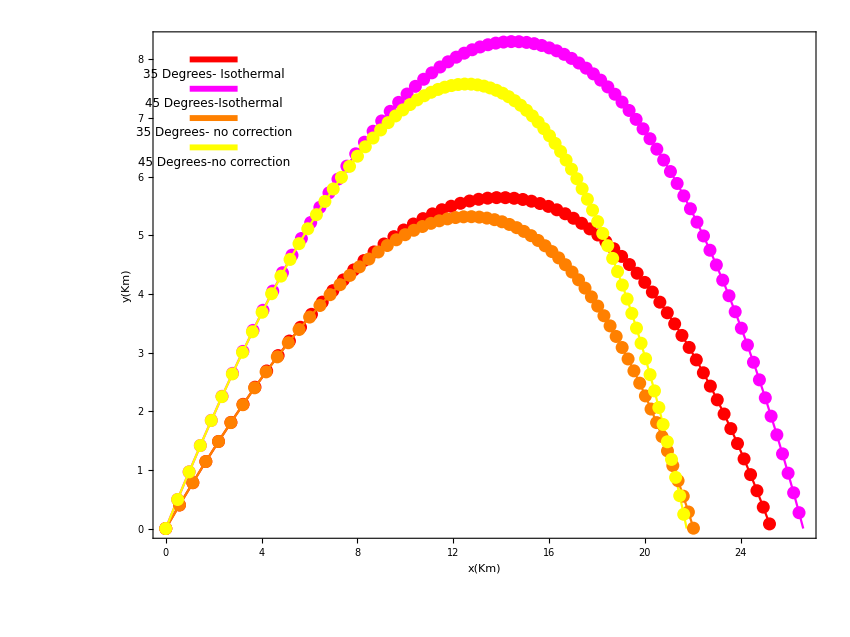

```mathematica
g3=Graphics[{Red,Thickness[0.005],Line[{{1,8},{3,8}}]}];
g4=Graphics[{Magenta,Thickness[0.005],Line[{{1,7.5},{3,7.5}}]}];
g32=Graphics[{Orange,Thickness[0.005],Line[{{1,7},{3,7}}]}];
g42=Graphics[{Yellow,Thickness[0.005],Line[{{1,6.5},{3,6.5}}]}];
Show[g3,g4,g32,g42,p7,p7a,p7a2,p72, PlotRange->All,Frame -> True,FrameLabel->{Style["x(Km)",Large],Style["y(Km)",Large]},LabelStyle->Directive[20,Black],ImageSize->850 ,AspectRatio->0.75,Epilog->{Inset[Style["35 Degrees- Isothermal",12],{2,7.75}], Inset[Style["45 Degrees-Isothermal",12] ,{2,7.25}],Inset[Style["35 Degrees- no correction",12],{2,6.75}], Inset[Style["45 Degrees-no correction",12] ,{2,6.25}]}]
```

The graph shows a match between the (solid) NDSolve values and the coded Euler (dotted)

## Problem 3b

Do not run this code without running 3a first since it depends on some output from there. This code is essentially the same but with a different b2m value so it’s no longer an exponential

```mathematica
a=6.5 10^-3; α=2.5;
p8 = Table[0,{i,lθ }];
p8a = Table[0,{i,lθ }];
T0=250;
Do[ 
vx0 = v0 Cos[θ[[nθ]]]; vy0 = v0 Sin[θ[[nθ]]];
vx3List = Table[0,{i,lt}]; vy3List = vx3List; x3List =vx3List;y3List = vx3List;b2m3List=vx3List;
vx3List[[1]] = vx0; vy3List[[1]] = vy0; 
x3List[[1]]   = x0;   y3List[[1]]    = y0; 
b2m3List[[1]]=b2m;

Do[
x3List[[nt]]   = x3List[[nt-1]] + vx3List[[nt-1]] dt; 
y3List[[nt]]   = y3List[[nt-1]] + vy3List[[nt-1]] dt;
v3Norm =  Sqrt[vx3List[[nt-1]]^2+vy3List[[nt-1]]^2];
vx3List[[nt]] =vx3List[[nt-1]] - (b2m3List[[nt-1]]* v3Norm*(vx3List[[nt-1]])* dt );
vy3List[[nt]] =vy3List[[nt-1]] - ((grav+(b2m3List[[nt-1]]*v3Norm*(vy3List[[nt-1]])))* dt );
(*the line below is where it differs from 3a*)
b2m3List[[nt]]=b2m*(1-(a y3List[[nt]])/T0)^α ;
If[y3List[[nt]]>0,n3Range = nt],{nt,2,lt}];
xy3List =Table[{x3List[[j]],y3List[[j]]},{j,n3Range}];
p53 =ListPlot[xy3List/1000.0,PlotStyle->color[[nθ+2]]];


solProj3 = NDSolve[{x3'[t]== vx3[t],y3'[t]==vy3[t], vx3'[t]==-b2m* (1-(a *y3[t])/T0)^α  *√((vx3[t])^2+(vy3[t])^2)*(vx3[t]),vy3'[t]== -b2m* (1-(a y3[t])/T0)^α  *√((vx3[t])^2+(vy3[t])^2)*vy3[t]-grav, x3[0]==x0, y3[0]==y0, vx3[0]== vx0, vy3[0]==vy0,WhenEvent[y3[t]== 0,end3 = t]},{x3,y3},{t,tmax},StartingStepSize->dt,Method->{"FixedStep",Method->"ExplicitEuler"}];

(*----------------------------------------------------------------------------------------------------------*)

p5b3 =ParametricPlot[Evaluate[{x3[t],y3[t]}/.solProj3]/1000.0,{t,0,end3},PlotStyle->color[[nθ+2]]];
p8a[[nθ]]=p5b3;
 p8[[nθ]] =p53,

{nθ,lθ}] (*every iteration adds the resultant p5 for a certain ndWind value to a list of list plots to combine them all in one plot*)
```

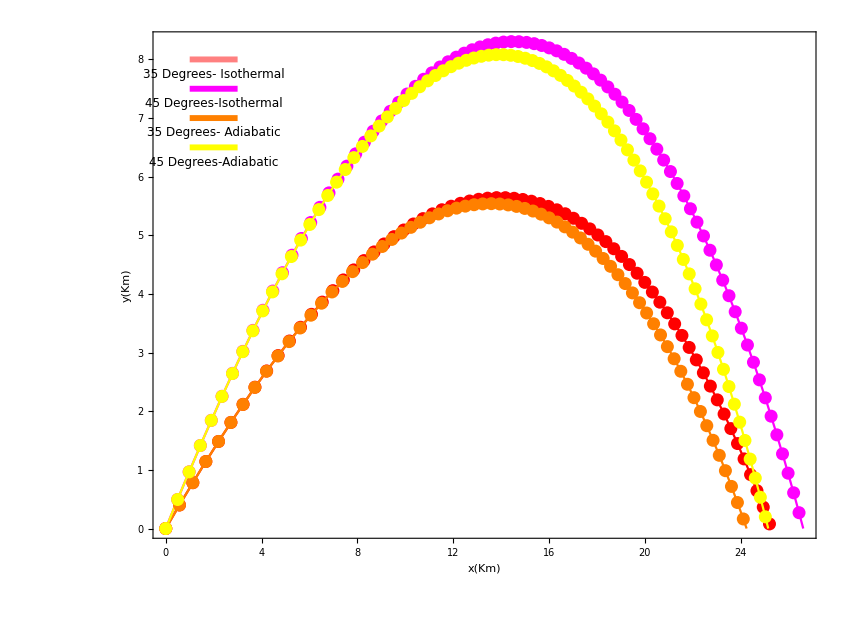

```mathematica
g3=Graphics[{Pink,Thickness[0.005],Line[{{1,8},{3,8}}]}];
g4=Graphics[{Magenta,Thickness[0.005],Line[{{1,7.5},{3,7.5}}]}];
g32=Graphics[{Orange,Thickness[0.005],Line[{{1,7},{3,7}}]}];
g42=Graphics[{Yellow,Thickness[0.005],Line[{{1,6.5},{3,6.5}}]}];
Show[g3,g4,g32,g42,p7,p7a,p8a,p8, PlotRange->All,Frame -> True,FrameLabel->{Style["x(Km)",Large],Style["y(Km)",Large]},LabelStyle->Directive[20,Black],ImageSize->850 ,AspectRatio->0.75,Epilog->{Inset[Style["35 Degrees- Isothermal",12],{2,7.75}], Inset[Style["45 Degrees-Isothermal",12] ,{2,7.25}],Inset[Style["35 Degrees- Adiabatic",12],{2,6.75}], Inset[Style["45 Degrees-Adiabatic",12] ,{2,6.25}]}]
```

The graph shows a match between the (solid) NDSolve values and the coded Euler (dotted)

## Problem 3c

```mathematica
ClearAll["Global`*"]
(* Initializations *) 
 color = {Red,Magenta,Orange,Yellow,Black};(*since we have 3 curves I'll pick 3 different colors*)
 grav = 9.8; tmax = 100; v0 = 700 ;
θ=45*(π/180.0) ; (*spent 3 hours looking for an error which tuned out to be a curly bracket around 45!!!!!!!!!! *)
b2m=4*10^-5;
yy=1*10^4;
x0 = 0.0; y0 =0.0; 
dt = 1;
(*Just the exact same code as part B for adiabatic correction but with different T values so I added T as a list and ran a do loop over the values and plotted*)
Tmp={250,275,300,325};
lTmp=Length[Tmp];
a=6.5 10^-3; α=2.5;
p8 = Table[0,{i,lTmp }];
p8a = Table[0,{i,lTmp }];
tList = Range[0,100,dt]; lt = Length[tList];
vx0 = v0 Cos[θ]; vy0 = v0 Sin[θ];

Do[ 
vx3List = Table[0,{i,lt}]; vy3List = vx3List; x3List =vx3List;y3List = vx3List;b2m3List=vx3List;
vx3List[[1]] = vx0; vy3List[[1]] = vy0; 
x3List[[1]]   = x0;   y3List[[1]]    = y0; 
b2m3List[[1]]=b2m;
Do[
x3List[[nt]]   = x3List[[nt-1]] + vx3List[[nt-1]] dt; 
y3List[[nt]]   = y3List[[nt-1]] + vy3List[[nt-1]] dt;
v3Norm =  Sqrt[vx3List[[nt-1]]^2+vy3List[[nt-1]]^2];
vx3List[[nt]] =vx3List[[nt-1]] - (b2m3List[[nt-1]]* v3Norm*(vx3List[[nt-1]])* dt );
vy3List[[nt]] =vy3List[[nt-1]] - ((grav+(b2m3List[[nt-1]]*v3Norm*(vy3List[[nt-1]])))* dt );
b2m3List[[nt]]=b2m*(1-(a y3List[[nt]])/Tmp[[nTmp]])^α; 

If[y3List[[nt]]>0,n3Range = nt],{nt,2,lt}];
xy3List =Table[{x3List[[j]],y3List[[j]]},{j,n3Range}];
p53 =ListPlot[xy3List/1000.0,PlotStyle->color[[nTmp]]];


solProj3 = NDSolve[{x3'[t]== vx3[t],y3'[t]==vy3[t], vx3'[t]==-b2m* (1-(a *y3[t])/Tmp[[nTmp]])^α  *√((vx3[t])^2+(vy3[t])^2)*(vx3[t]),vy3'[t]== -b2m* (1-(a y3[t])/Tmp[[nTmp]])^α  *√((vx3[t])^2+(vy3[t])^2)*vy3[t]-grav, x3[0]==x0, y3[0]==y0, vx3[0]== vx0, vy3[0]==vy0,WhenEvent[y3[t]== 0,end3 = t]},{x3,y3},{t,tmax},StartingStepSize->dt,Method->{"FixedStep",Method->"ExplicitEuler"}];

(*----------------------------------------------------------------------------------------------------------*)

p5b3 =ParametricPlot[Evaluate[{x3[t],y3[t]}/.solProj3]/1000.0,{t,0,end3},PlotStyle->color[[nTmp]]];
p8a[[nTmp]]=p5b3;
 p8[[nTmp]] =p53,

{nTmp,lTmp}]
```

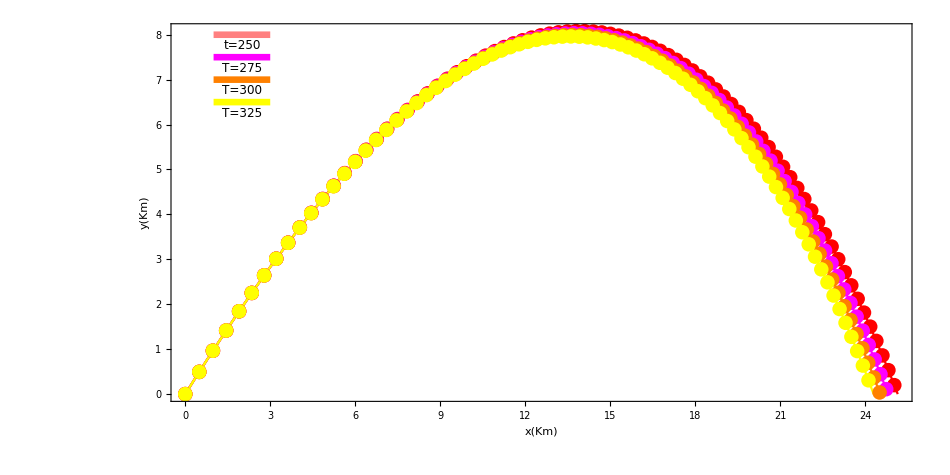

```mathematica
g3=Graphics[{Pink,Thickness[0.005],Line[{{1,8},{3,8}}]}];
g4=Graphics[{Magenta,Thickness[0.005],Line[{{1,7.5},{3,7.5}}]}];
g32=Graphics[{Orange,Thickness[0.005],Line[{{1,7},{3,7}}]}];
g42=Graphics[{Yellow,Thickness[0.005],Line[{{1,6.5},{3,6.5}}]}];
Show[g3,g4,g32,g42,p8a,p8, PlotRange->All,Frame -> True,FrameLabel->{Style["x(Km)",Large],Style["y(Km)",Large]},LabelStyle->Directive[20,Black],ImageSize->950 ,AspectRatio->0.5,Epilog->{Inset[Style["t=250",12],{2,7.75}], Inset[Style["T=275",12] ,{2,7.25}],Inset[Style["T=300",12],{2,6.75}], Inset[Style["T=325",12] ,{2,6.25}]}]
```

The graph shows a match between the (solid) NDSolve values and the coded Euler (dotted)